# Лабораторная работа №3

## Интерполяция и среднеквадратичное приближение функций

Михалькевич Д.Н.
гр. 221701

Вариант 8

## Задание 1.

```mathematica
f[x_]=Exp[2x-(2 x^2)/7]*ArcTan[(3 x^2)/14+5/6];
```

```mathematica
n=6;
```

```mathematica
a=0;
b=6;
h=(b-a)/n;
data=N[Table[{a+i h,f[a+i h]},{i,0,n}]];
```

```mathematica
Grid[data,Frame->All]
```

0. | 0.694738
1. | 4.4902
2. | 18.0492
3. | 37.7209
4. | 41.3258
5. | 24.5617
6. | 8.07549

```mathematica
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
```

### a) построить интерполяционный многочлен Лагранжа

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*Product[If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1],{j,1,Length[dataX]}];
Ln=LagrangeInterpolation[data[[All,1]],data[[All,2]],n+1]//Simplify
```

0.694738+14.4989 x-28.1172 x^2+23.8088 x^3-7.26886 x^4+0.914503 x^5-0.0407415 x^6

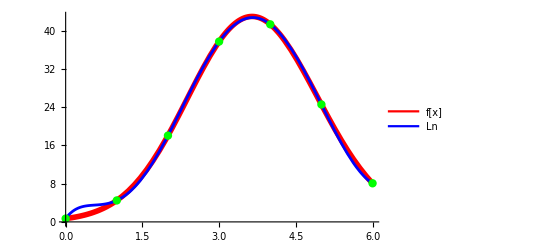

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Ln,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Ln"}]]
```

### б) создать таблицу конечных разностей функции f (x)

```mathematica
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=0]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=diff[i+1,k-1]-diff[i,k-1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
Grid[tab,Frame->All]
```

0.694738 | 3.79546 | 9.76356 | -3.65092 | -18.5285 | 36.4057 | -29.3339
4.4902 | 13.559 | 6.11264 | -22.1794 | 17.8772 | 7.07186 | 0
18.0492 | 19.6717 | -16.0668 | -4.3022 | 24.9491 | 0 | 0
37.7209 | 3.60489 | -20.369 | 20.6469 | 0 | 0 | 0
41.3258 | -16.7641 | 0.277907 | 0 | 0 | 0 | 0
24.5617 | -16.4862 | 0 | 0 | 0 | 0 | 0
8.07549 | 0 | 0 | 0 | 0 | 0 | 0

### в) построить второй интерполяционный многочлен Ньютона

```mathematica
findNewtonInter[dataX_,dataY_,deltaTab_,h_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-dataX[[n]])/h+k-1))/Factorial[i]*deltaTab[[n-i,i+1]]);
Pn=findNewtonInter[dataX,dataY,tab,h,n+1]//Simplify
```

0.694738+14.4989 x-28.1172 x^2+23.8088 x^3-7.26886 x^4+0.914503 x^5-0.0407415 x^6

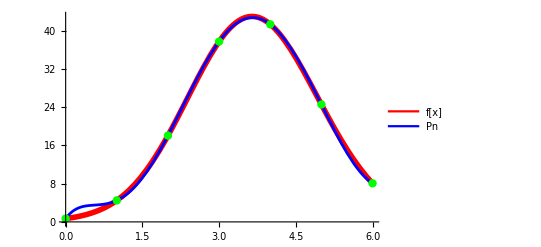

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pn,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pn"}]]
```

### г) построить интерполяционный многочлен Ньютона с помощью функции InterpolatingPolynomial

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np]
```

0.694738+14.4989 x-28.1172 x^2+23.8088 x^3-7.26886 x^4+0.914503 x^5-0.0407415 x^6

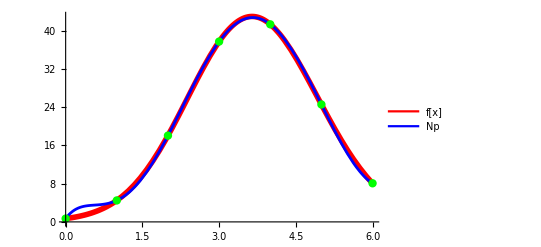

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Np,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Np"}]]
```

### д) вычислить значения функции и всех построенных интерполяционных членов

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Np/.x->2.4316
```

26.9215

27.2092

27.2092

27.2092

### е) построить график погрешности интерполирования многочленом Ньютона

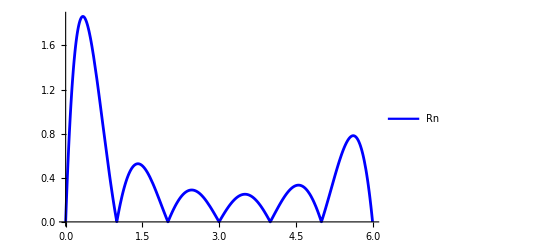

```mathematica
Rn=Abs[f[x]-Np];
graph1=Plot[Rn,{x,0,6},PlotStyle->Blue];
Legended[Show[graph1],LineLegend[{Blue},{"Rn"}]]
```

```mathematica
FindMaximum[{Rn,a<=x<=b},x]
```

{1.86248,{x→0.337594}}

```mathematica
ClearAll;
```

```mathematica
n=10;
```

```mathematica
a=0;
b=6;
h=(b-a)/n;
data=N[Table[{a+i h,f[a+i h]},{i,0,n}]];
```

```mathematica
Grid[data,Frame->All]
```

0. | 0.694738
0.6 | 2.21247
1.2 | 6.22067
1.8 | 14.3741
2.4 | 26.256
3. | 37.7209
3.6 | 42.947
4.2 | 39.0766
4.8 | 28.5897
5.4 | 16.8881
6. | 8.07549

```mathematica
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
```

### a) построить интерполяционный многочлен Лагранжа

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*Product[If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1],{j,1,Length[dataX]}];
Ln=LagrangeInterpolation[data[[All,1]],data[[All,2]],n+1]//Simplify
```

0.694738+2.76642 x-5.25299 x^2+13.4646 x^3-12.8941 x^4+8.22999 x^5-3.12782 x^6+0.678196 x^7-0.0824014 x^8+0.00519983 x^9-0.000131204 x^10

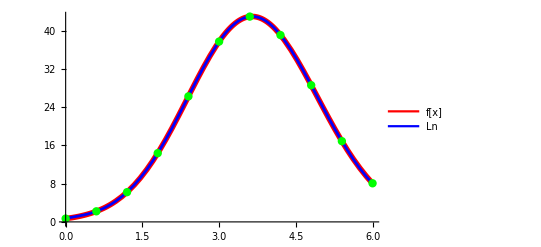

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Ln,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Ln"}]]
```

### б) создать таблицу конечных разностей функции f (x)

```mathematica
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=0]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=diff[i+1,k-1]-diff[i,k-1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
Grid[tab, Frame->All]
```

0.694738 | 1.51773 | 2.49048 | 1.65479 | -2.07164 | -1.65699 | 3.70943 | -1.12188 | -3.73162 | 6.06079 | -2.87888
2.21247 | 4.00821 | 4.14527 | -0.41685 | -3.72863 | 2.05245 | 2.58755 | -4.8535 | 2.32918 | 3.18191 | 0
6.22067 | 8.15348 | 3.72842 | -4.14548 | -1.67618 | 4.64 | -2.26594 | -2.52432 | 5.51109 | 0 | 0
14.3741 | 11.8819 | -0.417057 | -5.82165 | 2.96383 | 2.37406 | -4.79026 | 2.98677 | 0 | 0 | 0
26.256 | 11.4648 | -6.23871 | -2.85783 | 5.33789 | -2.4162 | -1.80349 | 0 | 0 | 0 | 0
37.7209 | 5.22613 | -9.09654 | 2.48006 | 2.92169 | -4.21969 | 0 | 0 | 0 | 0 | 0
42.947 | -3.87041 | -6.61648 | 5.40175 | -1.298 | 0 | 0 | 0 | 0 | 0 | 0
39.0766 | -10.4869 | -1.21473 | 4.10375 | 0 | 0 | 0 | 0 | 0 | 0 | 0
28.5897 | -11.7016 | 2.88902 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16.8881 | -8.8126 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8.07549 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

### в) построить второй интерполяционный многочлен Ньютона

```mathematica
findNewtonInter[dataX_,dataY_,deltaTab_,h_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-dataX[[n]])/h+k-1))/Factorial[i]*deltaTab[[n-i,i+1]]);
Pn=findNewtonInter[dataX,dataY,tab,h,n+1]//Simplify
```

0.694738+2.76642 x-5.25299 x^2+13.4646 x^3-12.8941 x^4+8.22999 x^5-3.12782 x^6+0.678196 x^7-0.0824014 x^8+0.00519983 x^9-0.000131204 x^10

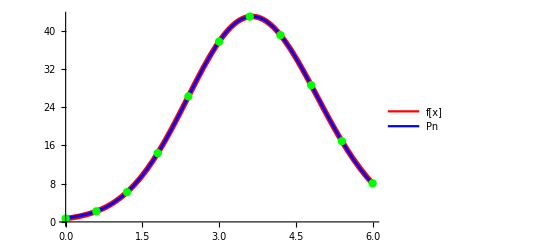

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pn,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pn"}]]
```

### г) построить интерполяционный многочлен Ньютона с помощью функции InterpolatingPolynomial

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np]
```

0.694738+2.76642 x-5.25299 x^2+13.4646 x^3-12.8941 x^4+8.22999 x^5-3.12782 x^6+0.678196 x^7-0.0824014 x^8+0.00519983 x^9-0.000131204 x^10

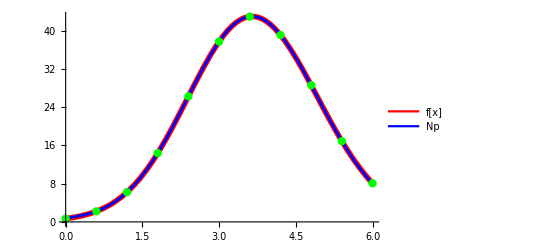

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Np,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Np"}]]
```

### д) вычислить значения функции и всех построенных интерполяционных членов

```mathematica
Print["f[2.4316]= ",f[2.4316]]
Print[ "Ln[2.4316]= ",Ln/.x->2.4316]
Print[ "Pn[2.4316]= ",Pn/.x->2.4316]
Print["Np[2.4316]= ",Np/.x->2.4316]
```

f[2.4316]= 26.9215

Ln[2.4316]= 26.9217

Pn[2.4316]= 26.9217

Np[2.4316]= 26.9217

### е) построить график погрешности интерполирования многочленом Ньютона

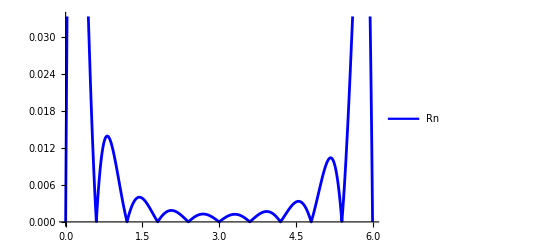

```mathematica
Rn=Abs[f[x]-Np];
graph1=Plot[Rn,{x,0,6},PlotStyle->Blue];
Legended[Show[graph1],LineLegend[{Blue},{"Rn"}]]
```

```mathematica
FindMaximum[{Rn,a<=x<=b},x]
```

{0.0139167,{x→0.813098}}

### ж) Увеличение количества узлов интерполяции привело к снижению погрешности интерполяции, что указывает на прямую зависимость точности интерполирования от числа узлов.

## Задание 2.

```mathematica
n=6;
```

```mathematica
For[i=0,i<=n,i++,Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(a+b)/2+(b-a)/2*Subscript[t, i];]
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
Grid[data,Frame->All]
```

5.92478 | 8.96065
5.34549 | 17.8712
4.30165 | 37.6296
3. | 37.7209
1.69835 | 12.674
0.654506 | 2.44561
0.0752163 | 0.807045

### a) создать таблицу разделенных разностей функции

```mathematica
findDividedDiff[dataX_,dataY_,first_,last_]:=If[first+1==last,(dataY[[last]]-dataY[[first]])/(dataX[[last]]-dataX[[first]]),(findDividedDiff[dataX,dataY,first+1,last]-findDividedDiff[dataX,dataY,first,last-1])/(dataX[[last]]-dataX[[first]])]
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=0]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=findDividedDiff[dataX,dataY,i+1,k+i+1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
Grid[tab,Frame->All]
```

8.96065 | -15.3819 | 2.18505 | 3.49609 | 0.867531 | 0.044576 | -0.0362799
17.8712 | -18.9285 | -8.04024 | -0.170478 | 0.632603 | 0.256798 | 0
37.6296 | -0.0701471 | -7.41849 | -3.13801 | -0.720794 | 0 | 0
37.7209 | 19.2424 | 4.0263 | -0.0916238 | 0 | 0 | 0
12.674 | 9.79875 | 4.29428 | 0 | 0 | 0 | 0
2.44561 | 2.82857 | 0 | 0 | 0 | 0 | 0
0.807045 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
diffRes=Table[diff[i,k],{i,0,n},{k,1,n}];
```

### б) построить интерполяционный многочлен Ньютона

```mathematica
findNewtonDividedDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=findNewtonDividedDiff[dataX,dataY,n,diffRes]//Simplify
```

0.146237+10.2329 x-20.6896 x^2+19.6905 x^3-6.26444 x^4+0.803726 x^5-0.0362799 x^6

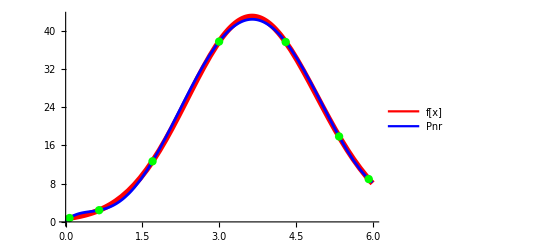

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pnr,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pnr"}]]
```

### в) построить интерполирующую функцию

```mathematica
Intf=Interpolation[data];
```

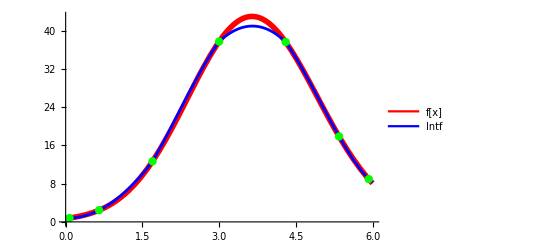

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Intf[x],{x,dataX[[n+1]],b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Intf"}]]
```

### г) вычислить значения функции и построенных интерполяционных многочленов

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print[ "Pnr[2.4316]= ",Pnr/.x->2.4316];
Print["Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 26.9215

Pnr[2.4316]= 27.6144

Intf[2.4316]= 27.4296

### д) найти максимумы абсолютных погрешностей интерполирования функции

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
Maximize[{AbsPnr[x],a<=x<=b},x]
```

{0.715443,{x→2.32743}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
Maximize[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},x]
```

{2.01529,{x→3.63449}}

### При n = 10

```mathematica
n=10;
For[i=0,i<=n,i++,Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(a+b)/2+(b-a)/2*Subscript[t, i];]
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
Grid[data,Frame->All]
```

5.96946 | 8.42713
5.7289 | 11.5679
5.26725 | 19.3243
4.62192 | 32.0811
3.8452 | 42.4385
3. | 37.7209
2.1548 | 21.1347
1.37808 | 8.16243
0.732751 | 2.81857
0.271104 | 1.18551
0.0305357 | 0.738418

### a) создать таблицу разделенных разностей функции

```mathematica
findDividedDiff[dataX_,dataY_,first_,last_]:=If[first+1==last,(dataY[[last]]-dataY[[first]])/(dataX[[last]]-dataX[[first]]),(findDividedDiff[dataX,dataY,first+1,last]-findDividedDiff[dataX,dataY,first,last-1])/(dataX[[last]]-dataX[[first]])]
Array[diff,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,diff[i,k]=0]];
For[i=0,i<=n,i++,diff[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
diff[i,k]=findDividedDiff[dataX,dataY,i+1,k+i+1]]];
tab=Array[diff,{n+1,n+1},{0,0}];
Grid[tab,Frame->All]
```

8.42713 | -13.0558 | 5.33429 | 1.96998 | -0.872839 | -0.377272 | -0.0107919 | 0.0222605 | 0.00646377 | 0.000656688 | -0.000111705
11.5679 | -16.8016 | 2.67966 | 3.82412 | 0.247458 | -0.336105 | -0.112998 | -0.0115884 | 0.00272173 | 0.0013201 | 0
19.3243 | -19.7679 | -4.52383 | 3.14883 | 1.44873 | 0.155531 | -0.0551009 | -0.026443 | -0.00480065 | 0 | 0
32.0811 | -13.3348 | -11.663 | -1.36026 | 0.843844 | 0.405386 | 0.0770123 | -0.00130339 | 0 | 0 | 0
42.4385 | 5.58173 | -8.30711 | -4.09755 | -0.73277 | 0.070319 | 0.0829967 | 0 | 0 | 0 | 0
37.7209 | 19.624 | 1.80205 | -1.81685 | -0.984097 | -0.246285 | 0 | 0 | 0 | 0 | 0
21.1347 | 16.7012 | 5.92129 | 0.868651 | -0.252761 | 0 | 0 | 0 | 0 | 0 | 0
8.16243 | 8.28086 | 4.28502 | 1.40558 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.81857 | 3.53746 | 2.39094 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.18551 | 1.8585 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.738418 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
diffRes=Table[diff[i,k],{i,0,n},{k,1,n}];
```

### б) построить интерполяционный многочлен Ньютона

```mathematica
findNewtonDividedDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=findNewtonDividedDiff[dataX,dataY,n,diffRes]//Simplify
```

0.685488+1.76152 x-1.12705 x^2+6.95728 x^3-7.53604 x^4+5.64755 x^5-2.36477 x^6+0.539365 x^7-0.0674256 x^8+0.00433954 x^9-0.000111705 x^10

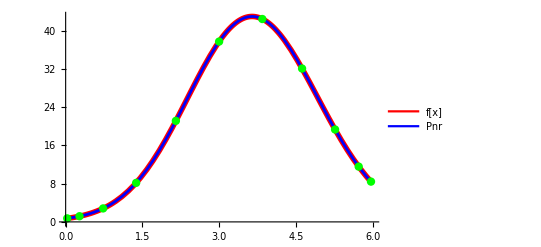

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Pnr,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Pnr"}]]
```

### в) построить интерполирующую функцию

```mathematica
Intf=Interpolation[data];
```

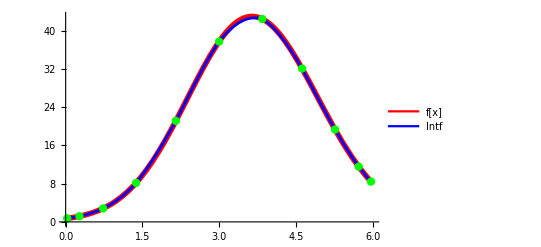

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Intf[x],{x,dataX[[n+1]],b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Intf"}]]
```

### г) вычислить значения функции и построенных интерполяционных многочленов

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Pnr[2.4316]= ",Pnr/. x->2.4316];
Print["Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 26.9215

Pnr[2.4316]= 26.9306

Intf[2.4316]= 26.9622

### д) найти максимумы абсолютных погрешностей интерполирования функции

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
Maximize[{AbsPnr[x],a<=x<=b},x]
```

{0.0101214,{x→1.03802}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
Maximize[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},x]
```

{0.449978,{x→3.42761}}

## Задание 3.

### По результатам 1 и 2 задания видно, что погрешность интерполирования зависит от числа узлов (чем больше узлов, тем выше точность) и от расположения их на отрезке (погрешность интерполирования многочленом степени n будет минимальной при использовании чебышевских узлов интерполяции по сравнению с равноотстоящими).

## Задание 4.

```mathematica
n=10;
h=b/n;
data=N[Table[{i h,f[i h]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 0.694738
0.6 | 2.21247
1.2 | 6.22067
1.8 | 14.3741
2.4 | 26.256
3. | 37.7209
3.6 | 42.947
4.2 | 39.0766
4.8 | 28.5897
5.4 | 16.8881
6. | 8.07549

### б) выполнить интерполяцию сплайном с помощью функции Interpolation

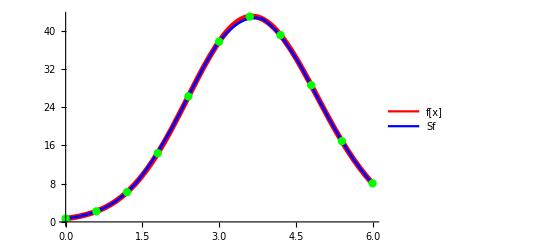

```mathematica
Sf=Interpolation[data,Method->"Spline"];
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Intf[x],{x,dataX[[n+1]],b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2, graph3],LineLegend[{Red,Blue},{"f[x]","Sf"}]]
```

### г) вычислить значения функции и построенных интерполяционных сплайнов

```mathematica
f[2.4316]
Sf[2.4316]
```

26.9215

26.9202

## Задание 5.

```mathematica
n=10;
b=6;
h=b/n;
data=N[Table[{i h,f[i h]},{i,0,n}]];
dataX=Table[data[[i,1]],{i,n+1}];
dataY=Table[data[[i,2]],{i,n+1}];
Grid[data,Frame->All]
```

0. | 0.694738
0.6 | 2.21247
1.2 | 6.22067
1.8 | 14.3741
2.4 | 26.256
3. | 37.7209
3.6 | 42.947
4.2 | 39.0766
4.8 | 28.5897
5.4 | 16.8881
6. | 8.07549

#### а) аппроксимировать с помощью метода наименьших квадратов функцию многочленом первой степени

9.87738+3.46681 x

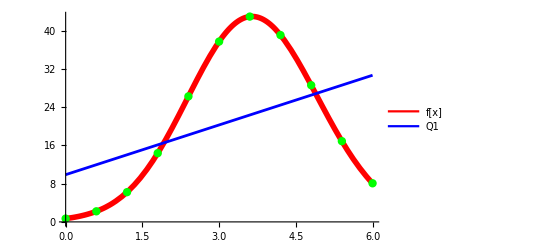

```mathematica
res=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,1}]];
polRes=0;
For[i=0,i<=1,i++,polRes=polRes+res[[i+1]]*x^i];
Q1=polRes
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q1,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q1"}]]
```

#### б) аппроксимировать с помощью метода наименьших квадратов функцию многочленом второй степени

-9.51762+25.0168 x-3.59167 x^2

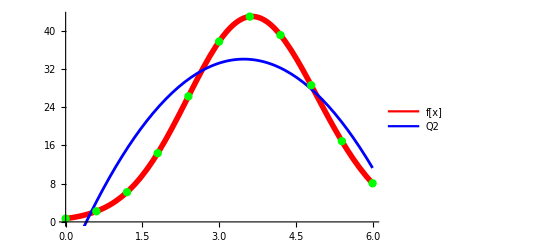

```mathematica
res=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,2}]];
polRes=0;
For[i=0,i<=2,i++,polRes=polRes+res[[i+1]]*x^i];
Q2=polRes
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q2,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q2"}]]
```

#### в) найти многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней

-1.40168+3.5246 x+5.80178 x^2-1.04372 x^3

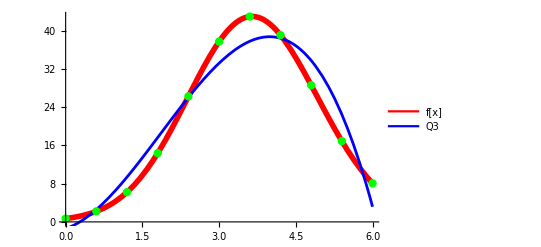

```mathematica
Q3=Fit[data,{1,x,x^2,x^3},x]
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q3,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q3"}]]
```

2.35026-18.188 x+23.8956 x^2-5.86874 x^3+0.402086 x^4

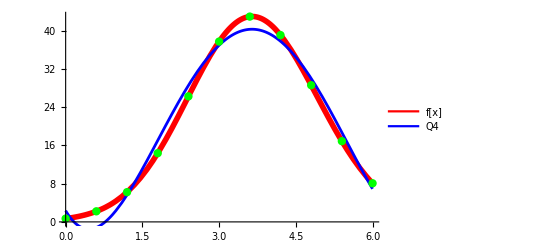

```mathematica
Q4=Fit[data,{1,x,x^2,x^3,x^4},x]
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.01]}];
graph2=Plot[Q4,{x,a,b},PlotStyle->Blue];
graph3=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3],LineLegend[{Red,Blue},{"f[x]","Q4"}]]
```

### д) вычислить значения функции и построенных многочленов

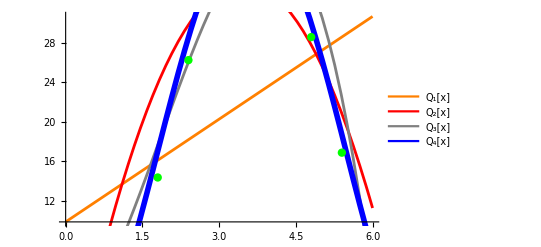

```mathematica
graph1=Plot[Q1,{x,a,b},PlotStyle->Orange];
graph2=Plot[Q2,{x,a,b},PlotStyle->Red];
graph3=Plot[Q3,{x,a,b},PlotStyle->Gray];
graph4=Plot[Q4,{x,a,b},PlotStyle->{Blue,Thickness[0.01]}];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Legended[Show[graph1,graph2,graph3,graph4,dots],LineLegend[{Orange,Red,Gray,Blue},{"Q_1[x]","Q_2[x]","Q_3[x]","Q_4[x]"}]]
```